```mathematica
h00 ={{0,t,0,0},{t,0,t, 0}, {0,t,0,t},{0,0,t,0}};
h01 ={{0,0,0,t}, {0,0,0,0}, {0,0,0,0},{0,0,0,0}};
h02 ={{0,0,0,0}, {0,0,0,0}, {0,0,0,0},{t,0,0,0}};
H0 =ArrayFlatten[{{h00,h01},{h02,h00}}];
{h00//TraditionalForm, h01//TraditionalForm, h02//TraditionalForm}
```

{(0 | t | 0 | 0
t | 0 | t | 0
0 | t | 0 | t
0 | 0 | t | 0),(0 | 0 | 0 | t
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
t | 0 | 0 | 0)}

```mathematica
H0//TraditionalForm
```

(0 | t | 0 | 0 | 0 | 0 | 0 | t
t | 0 | t | 0 | 0 | 0 | 0 | 0
0 | t | 0 | t | 0 | 0 | 0 | 0
0 | 0 | t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | 0 | 0
0 | 0 | 0 | 0 | t | 0 | t | 0
0 | 0 | 0 | 0 | 0 | t | 0 | t
t | 0 | 0 | 0 | 0 | 0 | t | 0)

```mathematica
(*中心原胞至右边原胞*)
```

```mathematica
h10 ={{0,0,0,0},{t,0,0, 0}, {0,0,0,t},{0,0,0,0}};
h11 ={{0,0,0,0}, {0,0,0,0}, {0,0,0,0},{0,0,0,0}};
h12 ={{0,0,0,0}, {0,0,0,0}, {0,0,0,0},{0,0,0,0}};
H1 =ArrayFlatten[{{h10,h11},{h12,h10}}];
```

```mathematica
{h10//TraditionalForm, h11//TraditionalForm, h12//TraditionalForm}
H1//TraditionalForm
```

{(0 | 0 | 0 | 0
t | 0 | 0 | 0
0 | 0 | 0 | t
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*中心原胞->左边相连原胞*)
```

```mathematica
h20 ={{0,t,0,0},{0,0,0, 0}, {0,0,0,0},{0,0,t,0}};
h21 ={{0,0,0,0}, {0,0,0,0}, {0,0,0,0},{0,0,0,0}};
h22 ={{0,0,0,0}, {0,0,0,0}, {0,0,0,0},{0,0,0,0}};
H2=ArrayFlatten[{{h20,h21},{h22,h20}}];
```

```mathematica
{h20//TraditionalForm, h21//TraditionalForm, h22//TraditionalForm}
H2//TraditionalForm
```

{(0 | t | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | t | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

(0 | t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | 0)

```mathematica
H = H0  + H1* E^(I*kx) + H2*E^(-I*kx); 
H//TraditionalForm
```

(0 | t+ⅇ^(-ⅈ kx) t | 0 | 0 | 0 | 0 | 0 | t
t+ⅇ^(ⅈ kx) t | 0 | t | 0 | 0 | 0 | 0 | 0
0 | t | 0 | t+ⅇ^(ⅈ kx) t | 0 | 0 | 0 | 0
0 | 0 | t+ⅇ^(-ⅈ kx) t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t+ⅇ^(-ⅈ kx) t | 0 | 0
0 | 0 | 0 | 0 | t+ⅇ^(ⅈ kx) t | 0 | t | 0
0 | 0 | 0 | 0 | 0 | t | 0 | t+ⅇ^(ⅈ kx) t
t | 0 | 0 | 0 | 0 | 0 | t+ⅇ^(-ⅈ kx) t | 0)

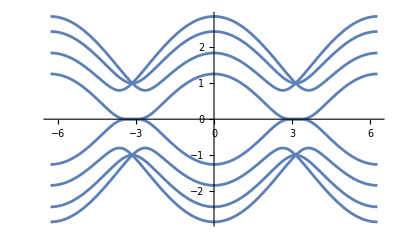

```mathematica
Plot[Eigenvalues[H/.{t->1}]//Sort, {kx, -2π, 2π}]
```

```mathematica
(*所取的原胞层数*)nslab=20;
(*中心原胞*)
h00={{0,t,0,0},{t,0,t,0},{0,t,0,t},{0,0,t,0}};
h01={{0,0,0,t},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
h02={{0,0,0,0},{0,0,0,0},{0,0,0,0},{t,0,0,0}};
H0=KroneckerProduct[IdentityMatrix[nslab],h00]+KroneckerProduct[DiagonalMatrix[Table[1,nslab-1],1],h01]+KroneckerProduct[DiagonalMatrix[Table[1,nslab-1],-1],h02];
(*中心原胞->右边相邻原胞*)
h10={{0,0,0,0},{t,0,0,0},{0,0,0,t},{0,0,0,0}};
h11={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
h12={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
H1=KroneckerProduct[IdentityMatrix[nslab],h10]+KroneckerProduct[DiagonalMatrix[Table[1,nslab-1],1],h11]+KroneckerProduct[DiagonalMatrix[Table[1,nslab-1],-1],h12];
(*中心原胞->左边相邻原胞*)
h20={{0,t,0,0},{0,0,0,0},{0,0,0,0},{0,0,t,0}};
h21={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
h22={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
H2=KroneckerProduct[IdentityMatrix[nslab],h20]+KroneckerProduct[DiagonalMatrix[Table[1,nslab-1],1],h21]+KroneckerProduct[DiagonalMatrix[Table[1,nslab-1],-1],h22];
(*总的H*)
H=H0+H1*E^(I*kx)+H2*E^(-I*kx);
```

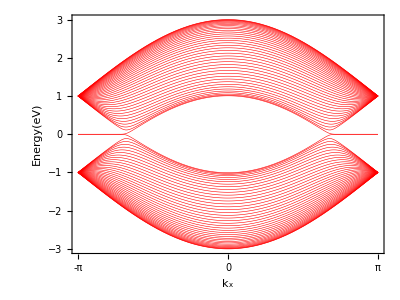

```mathematica
(*解析求解*)
Plot[Eigenvalues[H/.{t->1}]//Sort,{kx,-π,π},Axes->False,(*GridLines->{{-π,0,π},{0}},*)(*GridLinesStyle->Directive[Orange,Dashed],*)Frame->True,FrameTicks->{{Automatic,None},{{-π,0,π},None}},FrameStyle->Directive[Purple],FrameLabel->{"k_x","Energy(eV)"},PlotStyle->Directive[Red,Thickness[0.001]],AspectRatio->3/4,PlotRange->{{-π,π},{All,All}}]
```